```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

ECCE : the matrix elements are obtained in single-paricle-coordinate bases; hence, it is not the reduces mass but the single-particle mass that must be used for the factor of I_3, namely: ℏ^2/(2 m_N)

```mathematica
activeLEC=Import["./tmp.dat","Table"]
hbar=197.327053;
Mm=938.858;
μ=Mm/2;
mh2=(2 μ)/(hbar)^2;
Print[1/mh2]
```

{{#,L[fm^-1],C_0[nucl]},{4,-505.15},{6,-1090.55},{8,-1898.55},{10,-2934.2}}

41.4738

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2b2+4 lam))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{locall=lam},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

```mathematica
dimD=4;
logspace[increments_,start_?Positive,end_?Positive]:=Exp@Range[Log@start,Log@end,Log[end/start]/increments];

lamd=4;
LECc=Flatten[Select[activeLEC,#[[1]]==lamd&]][[2]]
```

-505.15

```mathematica
widths={};

nbrThreads=8;
nbrWidthSamples=80000;
minW=0.1;maxW=32;minWidthDiff=0.15;rndPrec=5;

Do[
widthLr=Sort[#]&/@RandomReal[{SetPrecision[minW,rndPrec+1],SetPrecision[maxW,rndPrec+1]},{nbrWidthSamples,dimD},WorkingPrecision->rndPrec];
widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>minWidthDiff&]&];
AppendTo[widths,widthL];
,{nn,nbrThreads}];

Print["λ = ",lamd,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",nbrThreads," parallel threads."]
opti={};
SetSharedVariable[opti];
ta=AbsoluteTime[];

ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
dimD=Length[wi];
hamm=Table[ham[2 lamd^0.5,wi[[i]],wi[[j]],LECc],{i,dimD},{j,dimD}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,dimD},{j,dimD}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[((eigsorted[[1]]<results)&&(eigsorted[[1]]>-2.2)&&(Im[eigsorted[[1]]]==0)),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
Print["Core ",nt," : ",e0,optSet];
AppendTo[opti,{e0,optSet}];
,{nt,nbrThreads}];

tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0];
Print["opt. basis: ",optSet];
Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@optSet];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
ListPlot[plotData,PlotRange->Full,PlotLegends->{"B(2) = "<>ToString[e0]}]
Put[optSet,"DimerCore_"<>ToString[lamd]<>".mmo"];
Put[e0,"E0_"<>ToString[lamd]<>".mmo"];
```

λ = 4   C_0(λ) = -505.15  #(width-set candidates) = 604512  in 8 parallel threads.

```mathematica
hamm=Table[ham[lamd,optSet[[All,2]][[i]],optSet[[All,2]][[j]],LECc],{i,dimD},{j,dimD}];
normm=Table[norm[optSet[[All,2]][[i]],optSet[[All,2]][[j]]],{i,dimD},{j,dimD}];
{eval,evec}=Eigensystem[{hamm,normm}];
eval
```

{863.829,114.049,11.0493,-2.06131}

```mathematica
e0files=FileNames["E0_*.lst",NotebookDirectory[],Infinity];
wffiles=FileNames["dimerWF_*.lst",NotebookDirectory[],Infinity];
pltDat={};pltLabs={};
Do[
dimerCore=Get[wffiles[[nFile]]];
e0Core=Get[e0files[[nFile]]];
AppendTo[pltLabs,e0Core];
JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@dimerCore];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];
plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
AppendTo[pltDat,plotData];
,{nFile,Length[e0files]}]
ListPlot[#&/@pltDat,PlotRange->Full,PlotLegends->{"B(2) = "<>ToString[#]&/@pltLabs}]
```

-Graphics-

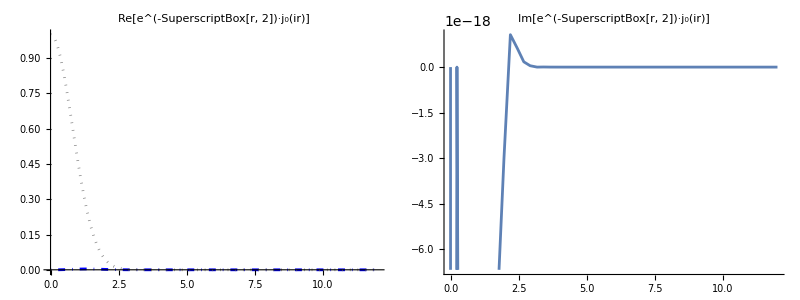

```mathematica
α=0.9;
rma=12;rmi=0.;
Grid[{{Plot[{√(π/(2  α r))BesselI[3.5,α r] Exp[-α r^2],Re[Exp[-α r^2] SphericalBesselJ[0,I α r]]},{r,rmi,rma},PlotLabel->"Re[e^(-SuperscriptBox[r, 2])·j_0(ir)]",ImageSize->Large,PlotRange->Full,PlotStyle->{Directive[Blue,DotDashed],Directive[Gray,Dotted]}],Plot[Im[Exp[-r^2] SphericalBesselJ[0,I r]],{r,rmi,rma},PlotLabel->"Im[e^(-SuperscriptBox[r, 2])·j_0(ir)]",ImageSize->Large]}}]
```